This is part of the construction of the proof of irrationality of √2 as per [1], p. 6, here reproduced:

Is the length of the diagonal of a square whose side is 1 expressible as a ratio of two integers? In other words, do there exist two integers a,b with no divisor in common such that (a/b)^2=2?
If a^2=2 b^2, then a must be even since 2 b^2 is even, and the square of an odd integer is odd. Therefore, a=2 a_1, where a_1 is again an integer. Thus 2 a^2=4 a_1^2=2 b^2, and we conclude by dividing by 2 that b must be even or b=2 b_1. But, we have assumed that the fraction a/b already has been brought to its simplest form; i.e., that a and b had no common factor. This contradiction shows the impossibility of representing √2 as a fraction.

We’ll “square” a number by intersecting a line perpendicular to its segment from one of its endpoints with the arc from the other endpoint.

The OO modeling of this construction is in the package pslab.geom.

Draw a segment from a to b.

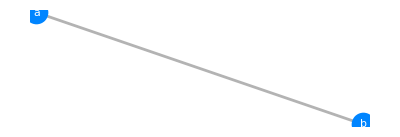

```mathematica
RandomInstance@GeometricScene[{a,b},{Line@{a,b}}]
```

Find the segment’s middle point.

```mathematica
segmentMidPoint=.;segmentMidPoint=Function[{a,b},
Block[{steps,l,c1,c2,i1},
	steps={};
	
	Print@"Find a line's middle point from a, b";
	
	l=Line@{a,b};
	c1=Circle[a,EuclideanDistance[a,b]];
	AppendTo[steps,GeometricScene[{a,b},{l,c1}]];
	Print@Labeled[RandomInstance@steps[[1]],"1. Draw a circle with center a and radius b - a",Top];
	Print@RandomInstance@steps[[1]];
	
	c2=Circle[b,EuclideanDistance[a,b]];
	AppendTo[steps,GeometricScene[{a,b},{l,c1,c2}]];
	(*Print@Labeled[RandomInstance@steps[[2]],"2. Draw a circle with center Cell["b",ExpressionUUID->"cd9216c7-a0ee-4651-a728-5cd2af76d7ab"] and radius b - a",Top];*)
	Print@RandomInstance@steps[[2]];
	
	i1=First@RegionIntersection[c1,c2];
	Print@GeometricScene@RegionIntersection[c1,c2]
	(*Print@i1;*)
	(*AppendTo[steps,GeometricScene[{a,b},{l,c1,c2,i1}]];
	Print@Labeled[RandomInstance@steps[[3]],"3. ",Top];*)
]];
```

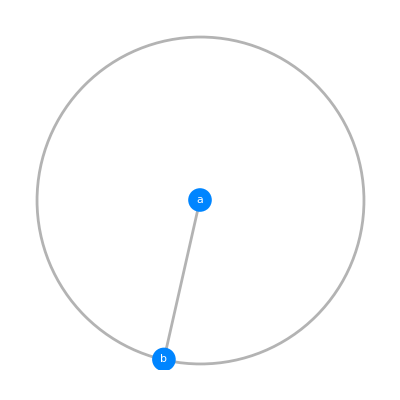

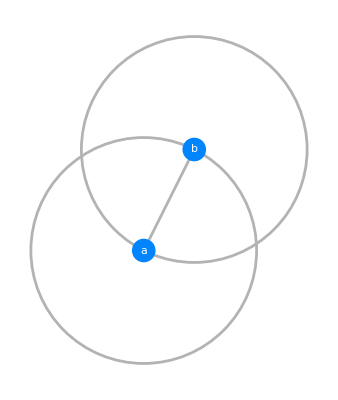

RegionIntersection[Circle[a,EuclideanDistance[a,b]],Circle[b,EuclideanDistance[a,b]]]

```mathematica
segmentMidPoint[a,b]
```

Find a line's middle point from a, b

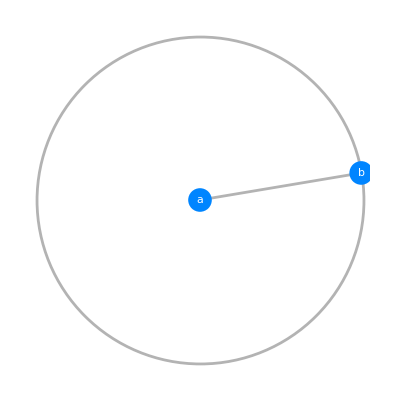
-Graphics-1. Draw a circle with center a and radius b - a

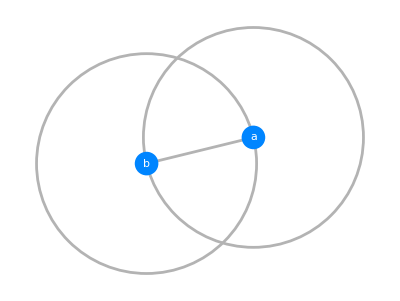
-Graphics-2. Draw a circle with center Cell["b"] and radius b - a

RegionIntersection[Circle[a,EuclideanDistance[a,b]],Circle[b,EuclideanDistance[a,b]]]

```mathematica
segmentMidPoint[a,b]
```

```mathematica
(Line[1,4])[[1]]
```

1

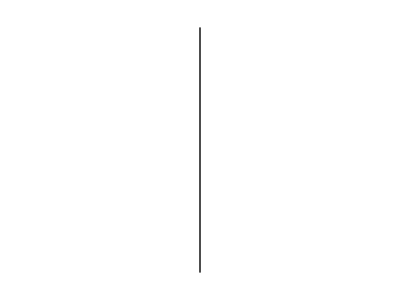

```mathematica
Block[{a,b,l,r,c1,c2,ml},
a={1,0};
b={4,0};
l=Line@{a,b};
r=EuclideanDistance[a,b];
c1=Circle[a,r];
c2=Circle[b,r];
(*ml=Line@*)
Graphics@Line@First@RegionIntersection[c1,c2]
]
```

```mathematica
RandomInstance@GeometricScene[{{a,b,c},{r}},{
l==Line[{a,b}],
c==Midpoint[{a,b}],
r==EuclideanDistance[a,b],
c1=Circle[a,r],
c2=Circle[b,r],
RegionIntersection[c1,c2]
}];
```

```mathematica
gs[a,b]
```

RandomInstance[GeometricScene[{{a,b,c},{r}},{l==Line[{a,b}],c==Midpoint[{a,b}],r==EuclideanDistance[a,b],c1=Circle[a,r],c2=Circle[b,r],-Graphics-},{}]]

```mathematica
gs[{1,0},{4,0}]
```

RandomInstance[GeometricScene[{{{1,0},{4,0},c},{r}},{l==Line[{{1,0},{4,0}}],c==Midpoint[{{1,0},{4,0}}],r==EuclideanDistance[{1,0},{4,0}],c1=Circle[{1,0},r],c2=Circle[{4,0},r],-Graphics-},{}]]

## References

1. Mathematics and Logic, Kac and Ulam, Dover Publications, 1968.